```mathematica
Quit[]
```

Use the local directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Define some functions and numeric k lattice, the lattice could be a subset to this set.

```mathematica
u=Function[{s,t},(s+t+1)/2];v=Function[{s,t},(-s+t+1)/2];
proj=Function[{u1,v1},(1/4) (4 v1^2-(1+v1^2-u1^2)^2) (1/4) (4 v1^2-(1+v1^2-u1^2)^2)];
ktable={0.01,0.025,0.063,0.158,0.4,0.6,1,1.39,2,2.4,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,25,27,30,33,35,37,40,45,50,56,62,68,74,80,88,96,102,110,120,130,140,155,170,185,200};
```

## Warm-up Example: Scale-invariant Primordial Spectrum

Define the 𝒫_ζ(k) or Δ_ζ^2(k), k is in arbitrary unit

```mathematica
pzeta=Function[x,1];
```

Compute the Ω_GW(k), noting that the extra factor 2 is for the defined lattice is actually a half of the full lattice, where the Z_2 symmetry of s interval is considered. It’s separated into two parts for the function is almost flat at large t, where a coarser lattice is sufficient.

```mathematica
GW=Table[k=ktable[[i]];
I2vsst15to50=Import["kernel//t15to50k"<>ToString[k]<>".mx"];(*change // to \\ if using non-Unix OS*)
I2vsst0to15=Import["kernel//t0to15k"<>ToString[k]<>".mx"];
GW1=First[ParallelSum[2/12(0.02)^2 (proj[u[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]],v[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]]]/(u[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]]^2 v[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]]^2)) Flatten[I2vsst0to15,1][[i]][[3]]pzeta[u[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]] k] pzeta[v[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]] k],{i,1,Dimensions[Flatten[I2vsst0to15,1]][[1]]}]];GW2=First[ParallelSum[2/12(0.05)^2 (proj[u[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]],v[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]]]/(u[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]]^2 v[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]]^2)) Flatten[I2vsst15to50,1][[i]][[3]]pzeta[u[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]] k] pzeta[v[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]] k],{i,1,Dimensions[Flatten[I2vsst15to50,1]][[1]]}]];GW1+GW2,{i,1,Length[ktable]}];(*takes ~30 min while running on 16 cores*)
```

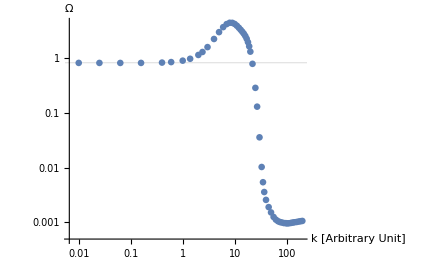

```mathematica
ListLogLogPlot[Transpose[{ktable,GW}],AxesLabel->{"k [Arbitrary Unit]", "Ω"},GridLines->{{},{0.824}},AxesStyle->Black]
```

## A Realistic Example: Scenario 2

```mathematica
invH0Mpc=4439867628.684654 10^-6;(*present 1/H0 in Mpc*)
rhoemd=0.0599862;(*total energy density at the onset of EMD, see figure 2*)
rhod=1.01536 10^-10;(*total energy density at the end of EMD, see figure 2*)
rhodtilde=2.58298204 10^-7;(*total energy density at the time of decay, see figure 2*)
f=28.93887589; (*these are the numeric results of Subscript[ρ, EMD], Subscript[ρ, d], OverTilde[Subscript[ρ, d]] and f is Subscript[r, d]=max(Subscript[ρ, mat]/Subscript[ρ, rad])*)
mpl=2.4 10^18; (*reduced Planck scale in GeV*)
H0gev=1.4376462716051872 10^-42;(*present H0 in GeV*)
T0=2.34464 10^-13;(*present CMB temperature in GeV*)
gstars0=3.92;(*present effective entropy degrees of freedom *)
gstarhi=106.75;(*effective degrees of freedom at above ~200 GeV*)
```

```mathematica
Hinf=4 10^13;(*in GeV*)
Trh=10^15;(*in GeV*)
chi0end=3 Hinf; mchi=√0.4 Hinf ;rhochiend=0.5 mchi^2 chi0end^2;
rhorh=π^2/30 110 Trh^4;(*the number 110 is just an approximation, it is UV dependent*)
rhoend= 3 Hinf^2 mpl^2/100;(*assuming a factor of 100 reduction in energy density, also model dependent*)
Vstar=3 Hinf^2 mpl^2;weff=0;
Nefolds=Log[(√π T0)/(√3 30^(1/4) H0gev)gstars0^(1/3)]+1/4 Log[Vstar^2/(mpl^4 rhoend)]+(1-3 weff)/(12(1+weff))Log[rhorh/rhoend]-1/12 Log[gstarhi]-1/12 Log[rhoemd/rhod];
kend=1/invH0Mpc E^Nefolds;
kemd=rhochiend/rhoend(rhorh/rhoend)^(1/6) kend;
kd=kemd (rhodtilde/rhoemd)^(1/6);
```

```mathematica
Nefolds
```

60.5754

```mathematica
kend
```

4.57278×10^22

```mathematica
kemd
```

5.43059×10^14

```mathematica
kd
```

6.92669×10^13

Define the primordial spectrum:

```mathematica
Pzetar=Function[x,E^3.044 10^-10 (x/0.05)^(0.9668-1)];(*Background constrained by planck*)
Pchi=Function[x,(Hinf/(π chi0end))^2 x^((2 mchi^2)/(3 Hinf^2))];
Pzetas2=Function[{kd,kemd,kend,f,x},0.8 Pzetar[x]+((f (kd^2/(x kemd)))/(4+3 f (kd^2/(x kemd))))^2 Pchi[x/kend]HeavisideTheta[x-kemd]+((f (kd/x)^2)/(4+3 f (kd/x)^2))^2 Pchi[x/kend]HeavisideTheta[x-kd]HeavisideTheta[kemd-x]+(f/(4+3 f))^2 Pchi[x/kend]HeavisideTheta[kd-x]];(*the factor 0.8 is a normalization factor chosen to ensure CMB and Lyα constraints are obeyed*)
```

Visualization:

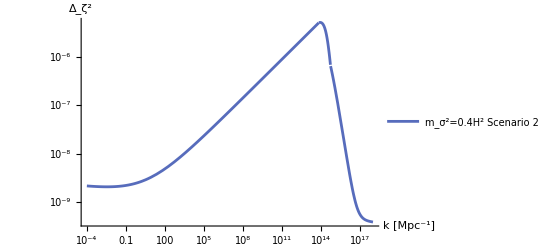

```mathematica
LogLogPlot[Pzetas2[kd,kemd,kend,f,x],{x,10^-4,10^18},PlotStyle->Directive[RGBColor[87/255,108/255,188/255]],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0]},PlotLegends->{"m_σ^2=0.4H^2 Scenario 2"},GridLines->{{kd},{10^-6}},AxesLabel->{"k [Mpc^-1]","Δ_ζ^2"}]
```

The semi-analytical pure radiation domination kernel result

```mathematica
u=Function[{s,t},(s+t+1)/2];v=Function[{s,t},(-s+t+1)/2];
im=Function[{u,v},(3/4)(1/(u^3 v^3))(u^2+v^2-3)];ic=Function[{u,v},π(u^2+v^2-3)HeavisideTheta[u+v-√3]];is=Function[{u,v},4 u v+(u^2+v^2-3)Log[Abs[(3-(u-v)^2)/(3-(u+v)^2)]]];
I2os=Function[{u1,v1,u2,v2},(1/2)im[u1,v1]im[u2,v2](ic[u1,v1]ic[u2,v2]+is[u1,v1]is[u2,v2])];
J2os=Function[{u1,v1,u2,v2},(1/4)(4 v1^2-(1+v1^2-u1^2)^2)(1/4)(4 v2^2-(1+v2^2-u2^2)^2)I2os[u1,v1,u2,v2]];
GWbare0S2=ParallelTable[{10^x,(2^2/48)NIntegrate[J2os[u[s,t],v[s,t],u[s,t],v[s,t]](Pzetas2[kd,kemd,kend,f,10^x u[s,t]]/u[s,t]^2)(Pzetas2[kd,kemd,kend,f,10^x v[s,t]]/v[s,t]^2),{s,-1,1},{t,0,∞},Method->{"MonteCarloRule","Points"->1 10^5}]},{x,9,16,0.1}];(*takes ~45 sec while running on 16 cores*)
```

Convert k in Mpc^-1 into f in Hz,and shiftΩ_GW(k)toΩ_(GW,0)(k)h^2

```mathematica
GWbareS2=Transpose[{ Transpose[GWbare0S2][[1]] (3 10^-3)/(1.9 10^12),Transpose[GWbare0S2][[2]] 4.2 10^-5 (3.36/106.75)^(1/3)}];
```

Conversion between physical units and numerical units: kd is a physical scale in Mpc^-1; kdnum is the conformal Hubble at the end of EMD in the numerical units; therefore to convert a k value from numerical units into Mpc^-1 units, we multiply k by kd/kdnum

```mathematica
kd=6.976676168844217*^13;
kdnum=14.4644;(*this is from the 0th-ord ODE system*)
kdex=kd/kdnum
```

4.82334×10^12

Let the Δ_ζ^2 be a single variable function for the conciseness and fit into the GW computation

```mathematica
pzeta=Function[x,Pzetas2[kd,kemd,kend,f,x]];
```

Compute the Ω_GW(k):

```mathematica
GW0S2=Table[k=ktable[[i]];
I2vsst15to50=Import["kernel//t15to50k"<>ToString[k]<>".mx"];(*change // to \\ if using non-Unix OS*)
I2vsst0to15=Import["kernel//t0to15k"<>ToString[k]<>".mx"];
GW1=First[ParallelSum[2/12(0.02)^2 (proj[u[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]],v[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]]]/(u[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]]^2 v[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]]^2)) Flatten[I2vsst0to15,1][[i]][[3]]pzeta[u[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]] k kdex] pzeta[v[Flatten[I2vsst0to15,1][[i]][[1]],Flatten[I2vsst0to15,1][[i]][[2]]] k kdex ],{i,1,Dimensions[Flatten[I2vsst0to15,1]][[1]]}]];GW2=First[ParallelSum[2/12(0.05)^2(proj[u[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]],v[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]]]/(u[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]]^2 v[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]]^2)) Flatten[I2vsst15to50,1][[i]][[3]]pzeta[u[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]] k kdex] pzeta[v[Flatten[I2vsst15to50,1][[i]][[1]],Flatten[I2vsst15to50,1][[i]][[2]]] k kdex ],{i,1,Dimensions[Flatten[I2vsst15to50,1]][[1]]}]];GW1+GW2,{i,1,Length[ktable]}];(*takes ~30 min while running on 16 cores*)
```

Convert k in Mpc^-1 into f in Hz, and shift Ω_GW(k) to Ω_(GW,0)(k)h^2

```mathematica
GWS2=Transpose[{ktable kdex (3 10^-3)/(1.9 10^12),GW0S2 4.2 10^-5 (3.36/106.75)^(1/3)}];
```

Visualize

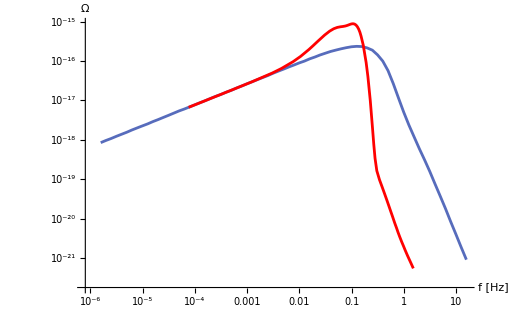

```mathematica
ListLogLogPlot[{GWbareS2,GWS2},PlotStyle->{Directive[RGBColor[87/255,108/255,188/255]],Directive[RGBColor[255/255,1/255,1/255]]},LabelStyle->{FontFamily->"Times New Roman",25,GrayLevel[0]},Joined->True,AxesLabel->{"f [Hz]","Ω"}]
```